```mathematica
(*Directory[]*)
```

C:\Users\mariana\Documents

```mathematica
(*DirectoryName["C:\\Users\\mariana\\Desktop\\LastPictures\\Reactive\\5%\\6M\\1\\image005.jpg"]*)
```

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\

```mathematica
dir1="C:\\Users\\mariana\\Desktop\\LastPictures\\Reactive\\5%\\6M\\"<>"1\\"
```

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\

```mathematica
SetDirectory[dir1]
```

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1

```mathematica
list=FileNames["*.jpg"];
```

```mathematica
Length[list]
```

36

```mathematica
(*FileNameJoin[{dir1, "image005.jpg"}]*)
```

```mathematica
"C:\\Users\\mariana\\Desktop\\LastPictures\\Reactive\\5%\\6M\\1\\image005.jpg"
```

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image005.jpg

```mathematica
img=Import["C:\\Users\\mariana\\Desktop\\LastPictures\\Reactive\\5%\\6M\\1\\image005.jpg"]
```

-Graphics-

```mathematica
"C:\\Users\\mariana\\Desktop\\LastPictures\\Reactive\\5%\\6M\\"<>"1\\"
```

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\

```mathematica
img1=Import["C:\\Users\\mariana\\Desktop\\LastPictures\\Reactive\\5%\\6M\\1\\image005.jpg"]
```

-Graphics-

```mathematica
Bkg=Import["C:\\Users\\mariana\\Desktop\\LastPictures\\Reactive\\5%\\6M\\1\\image001.jpg"];
```

```mathematica
imgD=ImageDifference[img1,Bkg]
```

-Graphics-

```mathematica
(*imgDR=ImageRotate[imgD, Right];*)
```

```mathematica
imgDRBinary=Binarize[imgD]
```

-Graphics-

```mathematica
ImageMultiply[imgD,imgDRBinary]
```

-Graphics-

```mathematica
databn=ImageData[imgDRBinary];
```

```mathematica
{r,g,b}=ColorSeparate[imgD]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{w,h}=ImageDimensions[imgD]
```

{2136,3216}

```mathematica
data=ImageData[r,"Byte"];
```

```mathematica
datag=ImageData[g,"Byte"];
```

```mathematica
datab=ImageData[b,"Byte"];
```

```mathematica
(*Radius of the thermal as a function of the vertical distance, b*)
For[i=1,i<h+1,i=i+1,	
rb[i]=Dot[databn[[i]],Table[1,{i,1,w}]]/2;
rbd[i]=If[rb[i]≠0, rb[i]*2,1];
bRed[i]=Dot[databn[[i]],data[[i]]];
bGreen[i]=Dot[databn[[i]],datag[[i]]];
bBlue[i]=Dot[databn[[i]],datab[[i]]];

CbRed[i]=bRed[i]/rbd[i];
CbGreen[i]=bGreen[i]/rbd[i];
CbBlue[i]=bBlue[i]/rbd[i];
]
```

Null

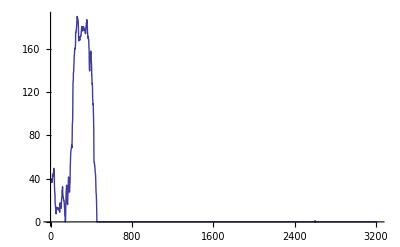
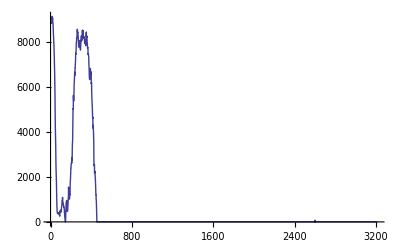
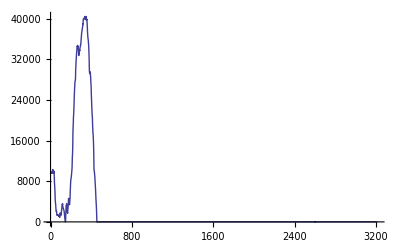
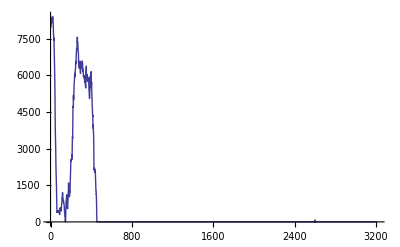
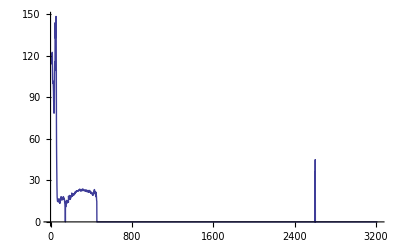
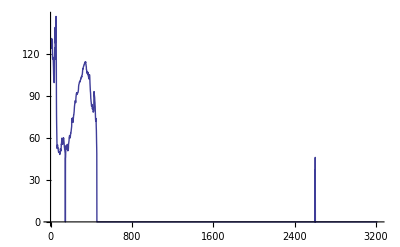
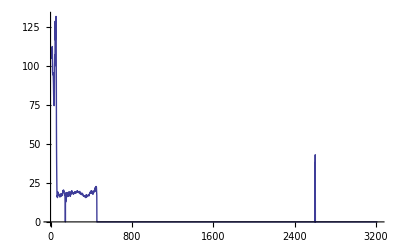

```mathematica
{lr,lR,lG,lB,lCrRed,lCrGreen,lCrBlue}={ListLinePlot[Table[rb[i],{i,1,h}]],ListLinePlot[Table[bRed[i],{i,1,h}]],ListLinePlot[Table[bGreen[i],{i,1,h}]],ListLinePlot[Table[bBlue[i],{i,1,h}]],ListLinePlot[Table[CbRed[i],{i,1,h}]],ListLinePlot[Table[CbGreen[i],{i,1,h}]],ListLinePlot[Table[CbBlue[i],{i,1,h}]]}
```

```mathematica
(*Radius of the thermal as a function of the horizontal distance, a*)
For[j=1,j<w+1,j=j+1,	
ra[j]=Dot[databn[[All,j]],Table[1,{i,1,h}]]/2;
rad[j]=If[ra[j]≠0, ra[j]*2,1];
aRed[j]=Dot[databn[[All,j]],data[[All,j]]];
aGreen[j]=Dot[databn[[All,j]],datag[[All,j]]];
aBlue[j]=Dot[databn[[All,j]],datab[[All,j]]];

CaRed[j]=aRed[j]/rad[j];
CaGreen[j]=aGreen[j]/rad[j];
CaBlue[j]=aBlue[j]/rad[j];
]
```

Null

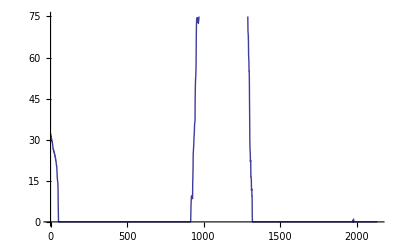
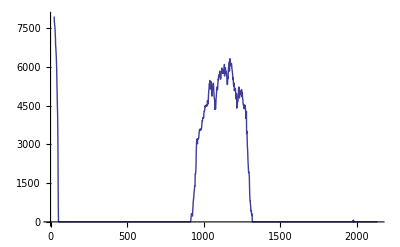
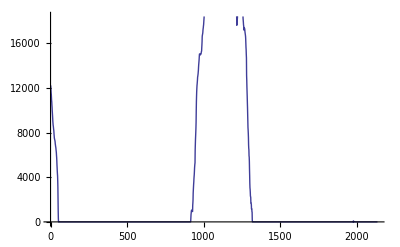
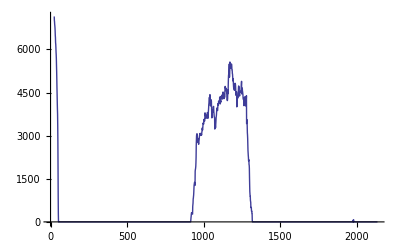
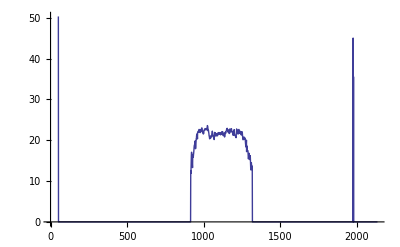
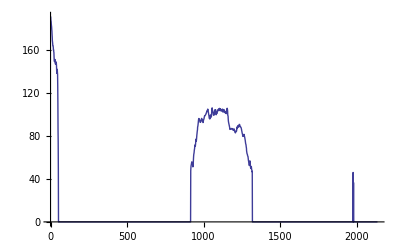
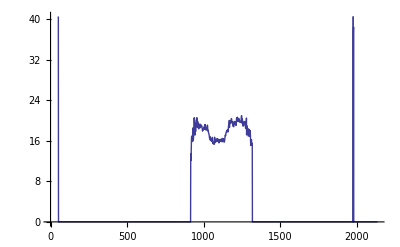

```mathematica
{lr,lR,lG,lB,lCrRed,lCrGreen,lCrBlue}={ListLinePlot[Table[ra[i],{i,1,h}]],ListLinePlot[Table[aRed[i],{i,1,h}]],ListLinePlot[Table[aGreen[i],{i,1,h}]],ListLinePlot[Table[aBlue[i],{i,1,h}]],ListLinePlot[Table[CaRed[i],{i,1,h}]],ListLinePlot[Table[CaGreen[i],{i,1,h}]],ListLinePlot[Table[CaBlue[i],{i,1,h}]]}
```

```mathematica
(* Area calculation using 2 different estimates*)
```

```mathematica
Area=Dot[Table[rb[i],{i,1,h}],Table[1,{i,1,h}]]
```

82851/2

```mathematica
TotalRed=Dot[Table[bRed[i],{i,1,h}],Table[1,{i,1,h}]]
```

2107638

```mathematica
TotalGreen=Dot[Table[bGreen[i],{i,1,h}],Table[1,{i,1,h}]]
```

7799604

```mathematica
TotalBlue=Dot[Table[bBlue[i],{i,1,h}],Table[1,{i,1,h}]]
```

1808591

```mathematica
maxb=Max[Table[rb[i],{i,1,h}]]
```

190

```mathematica
CtRed=TotalRed/Area
```

1405092/27617

```mathematica
CtGreen=TotalGreen/Area
```

5199736/27617

```mathematica
CtBlue=TotalBlue/Area
```

3617182/82851

```mathematica
For[i=h,i>0,i=i-1,
If[rb[i]/maxb>0.01,fp=i;i=0]]
```

```mathematica
fp
```

455